## Definitions

```mathematica
Sx={{0,(√3)/2,0,0},{(√3)/2,0,1,0},{0,1,0,(√3)/2},{0,0,(√3)/2,0}};
Sy={{0,(√3)/(2ⅈ),0,0},{(√3)/(-2ⅈ),0,1/ⅈ,0},{0,-1/ⅈ,0,(√3)/(2ⅈ)},{0,0,(-√3)/(2ⅈ),0}};
Sz={{3/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-3/2}};
Γx=Sx.Sx.Sx-41/20 Sx;
Γy=Sy.Sy.Sy-41/20 Sy;
Γz=Sz.Sz.Sz-41/20 Sz;
```

```mathematica
Sx//MatrixForm
Sy//MatrixForm
Sz//MatrixForm
Γx//MatrixForm
Γy//MatrixForm
Γz//MatrixForm
```

(0 | (√3)/2 | 0 | 0
(√3)/2 | 0 | 1 | 0
0 | 1 | 0 | (√3)/2
0 | 0 | (√3)/2 | 0)

(0 | -(ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -(ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 0)

(3/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -3/2)

(0 | -(3 √3)/20 | 0 | 3/4
-(3 √3)/20 | 0 | 9/20 | 0
0 | 9/20 | 0 | -(3 √3)/20
3/4 | 0 | -(3 √3)/20 | 0)

(0 | (3 ⅈ √3)/20 | 0 | (3 ⅈ)/4
-(3 ⅈ √3)/20 | 0 | -(9 ⅈ)/20 | 0
0 | (9 ⅈ)/20 | 0 | (3 ⅈ √3)/20
-(3 ⅈ)/4 | 0 | -(3 ⅈ √3)/20 | 0)

(3/10 | 0 | 0 | 0
0 | -9/10 | 0 | 0
0 | 0 | 9/10 | 0
0 | 0 | 0 | -3/10)

```mathematica
Tr[Sx.Sx]
Tr[Sx.Γx]
Tr[Γx.Γx]
Tr[Sx.Sy]
Tr[Γx.Γy]
Tr[Sx.Γy]
```

5

0

9/5

0

0

0

```mathematica
H1[δ_,kx_,ky_,kz_]:=δ(kx Γx+ky Γy+kz Γz)+(kx Sx+ky Sy+kz Sz);
H1[δ,kx,ky,kz]//MatrixForm
```

((3 kz)/2+(3 kz δ)/10 | (√3 kx)/2-1/2 ⅈ √3 ky+(-(3 √3 kx)/20+3/20 ⅈ √3 ky) δ | 0 | ((3 kx)/4+(3 ⅈ ky)/4) δ
(√3 kx)/2+1/2 ⅈ √3 ky+(-(3 √3 kx)/20-3/20 ⅈ √3 ky) δ | kz/2-(9 kz δ)/10 | kx-ⅈ ky+((9 kx)/20-(9 ⅈ ky)/20) δ | 0
0 | kx+ⅈ ky+((9 kx)/20+(9 ⅈ ky)/20) δ | -kz/2+(9 kz δ)/10 | (√3 kx)/2-1/2 ⅈ √3 ky+(-(3 √3 kx)/20+3/20 ⅈ √3 ky) δ
((3 kx)/4-(3 ⅈ ky)/4) δ | 0 | (√3 kx)/2+1/2 ⅈ √3 ky+(-(3 √3 kx)/20-3/20 ⅈ √3 ky) δ | -(3 kz)/2-(3 kz δ)/10)

```mathematica
H2[δ_,kx_,ky_,kz_]:=(kx Γx+ky Γy+kz Γz)+δ (kx Sx+ky Sy+kz Sz);
H2[δ,kx,ky,kz]//MatrixForm
```

((3 kz)/10+(3 kz δ)/2 | -(3 √3 kx)/20+3/20 ⅈ √3 ky+((√3 kx)/2-1/2 ⅈ √3 ky) δ | 0 | (3 kx)/4+(3 ⅈ ky)/4
-(3 √3 kx)/20-3/20 ⅈ √3 ky+((√3 kx)/2+1/2 ⅈ √3 ky) δ | -(9 kz)/10+(kz δ)/2 | (9 kx)/20-(9 ⅈ ky)/20+(kx-ⅈ ky) δ | 0
0 | (9 kx)/20+(9 ⅈ ky)/20+(kx+ⅈ ky) δ | (9 kz)/10-(kz δ)/2 | -(3 √3 kx)/20+3/20 ⅈ √3 ky+((√3 kx)/2-1/2 ⅈ √3 ky) δ
(3 kx)/4-(3 ⅈ ky)/4 | 0 | -(3 √3 kx)/20-3/20 ⅈ √3 ky+((√3 kx)/2+1/2 ⅈ √3 ky) δ | -(3 kz)/10-(3 kz δ)/2)

```mathematica
PropagatorS1[δ_,ω_,kx_,ky_,kz_]:=Inverse[-ⅈ ω IdentityMatrix[4]+H1[δ,kx,ky,kz]];
Factor[Simplify[PropagatorS1[0,ω,kx,ky,kz]]]//MatrixForm
```

((2 (9 kx^2 kz+9 ky^2 kz+3 kz^3+14 ⅈ kx^2 ω+14 ⅈ ky^2 ω+2 ⅈ kz^2 ω+12 kz ω^2+8 ⅈ ω^3))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | (2 √3 (kx-ⅈ ky) (3 kx^2+3 ky^2-3 kz^2-8 ⅈ kz ω+4 ω^2))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | -(4 √3 (kx-ⅈ ky)^2 (3 kz+2 ⅈ ω))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | -(12 (kx-ⅈ ky)^3)/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2))
(2 √3 (kx+ⅈ ky) (3 kx^2+3 ky^2-3 kz^2-8 ⅈ kz ω+4 ω^2))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | (2 (3 kz-2 ⅈ ω) (-3 kx^2-3 ky^2+3 kz^2+8 ⅈ kz ω-4 ω^2))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | (4 (kx-ⅈ ky) (3 kz-2 ⅈ ω) (3 kz+2 ⅈ ω))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | (4 √3 (kx-ⅈ ky)^2 (3 kz-2 ⅈ ω))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2))
-(4 √3 (kx+ⅈ ky)^2 (3 kz+2 ⅈ ω))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | (4 (kx+ⅈ ky) (3 kz-2 ⅈ ω) (3 kz+2 ⅈ ω))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | -(2 (3 kz+2 ⅈ ω) (-3 kx^2-3 ky^2+3 kz^2-8 ⅈ kz ω-4 ω^2))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | (2 √3 (kx-ⅈ ky) (3 kx^2+3 ky^2-3 kz^2+8 ⅈ kz ω+4 ω^2))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2))
-(12 (kx+ⅈ ky)^3)/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | (4 √3 (kx+ⅈ ky)^2 (3 kz-2 ⅈ ω))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | (2 √3 (kx+ⅈ ky) (3 kx^2+3 ky^2-3 kz^2+8 ⅈ kz ω+4 ω^2))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)) | -(2 (9 kx^2 kz+9 ky^2 kz+3 kz^3-14 ⅈ kx^2 ω-14 ⅈ ky^2 ω-2 ⅈ kz^2 ω+12 kz ω^2-8 ⅈ ω^3))/((kx^2+ky^2+kz^2+4 ω^2) (9 kx^2+9 ky^2+9 kz^2+4 ω^2)))

```mathematica
PropagatorS2[δ_,ω_,kx_,ky_,kz_]:=Inverse[-ⅈ ω IdentityMatrix[4]+H2[δ,kx,ky,kz]];
PropagatorS2[0,ω,kx,ky,kz]//MatrixForm
```

(((243 kx^2 kz)/2000+(243 ky^2 kz)/2000+(243 kz^3)/1000+27/100 ⅈ kx^2 ω+27/100 ⅈ ky^2 ω+81/100 ⅈ kz^2 ω+(3 kz ω^2)/10+ⅈ ω^3)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | ((81 √3 kx^3)/2000+81/500 ⅈ √3 kx^2 ky-81/500 √3 kx ky^2-(81 ⅈ √3 ky^3)/2000-(81 √3 kx kz^2)/2000+(81 ⅈ √3 ky kz^2)/2000-9/100 ⅈ √3 kx kz ω-9/100 √3 ky kz ω-3/20 √3 kx ω^2+3/20 ⅈ √3 ky ω^2)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | ((243 √3 kx^2 kz)/2000+81/500 ⅈ √3 kx ky kz-(243 √3 ky^2 kz)/2000+9/50 ⅈ √3 kx^2 ω-9/100 √3 kx ky ω-9/50 ⅈ √3 ky^2 ω)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | ((243 kx^3)/2000+(243 ⅈ kx^2 ky)/1000+(243 kx ky^2)/1000+(243 ⅈ ky^3)/2000+(243 kx kz^2)/400+243/400 ⅈ ky kz^2+(3 kx ω^2)/4+3/4 ⅈ ky ω^2)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4)
((81 √3 kx^3)/2000-81/500 ⅈ √3 kx^2 ky-81/500 √3 kx ky^2+(81 ⅈ √3 ky^3)/2000-(81 √3 kx kz^2)/2000-(81 ⅈ √3 ky kz^2)/2000-9/100 ⅈ √3 kx kz ω+9/100 √3 ky kz ω-3/20 √3 kx ω^2-3/20 ⅈ √3 ky ω^2)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | (-(1053 kx^2 kz)/2000-(1053 ky^2 kz)/2000-(81 kz^3)/1000+63/100 ⅈ kx^2 ω+63/100 ⅈ ky^2 ω+9/100 ⅈ kz^2 ω-(9 kz ω^2)/10+ⅈ ω^3)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | ((81 kx^3)/400-81/200 ⅈ kx^2 ky+(81 kx ky^2)/200-(81 ⅈ ky^3)/400+(81 kx kz^2)/2000-(81 ⅈ ky kz^2)/2000+(9 kx ω^2)/20-9/20 ⅈ ky ω^2)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | (-(243 √3 kx^2 kz)/2000-81/500 ⅈ √3 kx ky kz+(243 √3 ky^2 kz)/2000+9/50 ⅈ √3 kx^2 ω-9/100 √3 kx ky ω-9/50 ⅈ √3 ky^2 ω)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4)
((243 √3 kx^2 kz)/2000-81/500 ⅈ √3 kx ky kz-(243 √3 ky^2 kz)/2000+9/50 ⅈ √3 kx^2 ω+9/100 √3 kx ky ω-9/50 ⅈ √3 ky^2 ω)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | ((81 kx^3)/400+81/200 ⅈ kx^2 ky+(81 kx ky^2)/200+(81 ⅈ ky^3)/400+(81 kx kz^2)/2000+(81 ⅈ ky kz^2)/2000+(9 kx ω^2)/20+9/20 ⅈ ky ω^2)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | ((1053 kx^2 kz)/2000+(1053 ky^2 kz)/2000+(81 kz^3)/1000+63/100 ⅈ kx^2 ω+63/100 ⅈ ky^2 ω+9/100 ⅈ kz^2 ω+(9 kz ω^2)/10+ⅈ ω^3)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | ((81 √3 kx^3)/2000+81/500 ⅈ √3 kx^2 ky-81/500 √3 kx ky^2-(81 ⅈ √3 ky^3)/2000-(81 √3 kx kz^2)/2000+(81 ⅈ √3 ky kz^2)/2000+9/100 ⅈ √3 kx kz ω+9/100 √3 ky kz ω-3/20 √3 kx ω^2+3/20 ⅈ √3 ky ω^2)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4)
((243 kx^3)/2000-(243 ⅈ kx^2 ky)/1000+(243 kx ky^2)/1000-(243 ⅈ ky^3)/2000+(243 kx kz^2)/400-243/400 ⅈ ky kz^2+(3 kx ω^2)/4-3/4 ⅈ ky ω^2)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | (-(243 √3 kx^2 kz)/2000+81/500 ⅈ √3 kx ky kz+(243 √3 ky^2 kz)/2000+9/50 ⅈ √3 kx^2 ω+9/100 √3 kx ky ω-9/50 ⅈ √3 ky^2 ω)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | ((81 √3 kx^3)/2000-81/500 ⅈ √3 kx^2 ky-81/500 √3 kx ky^2+(81 ⅈ √3 ky^3)/2000-(81 √3 kx kz^2)/2000-(81 ⅈ √3 ky kz^2)/2000+9/100 ⅈ √3 kx kz ω-9/100 √3 ky kz ω-3/20 √3 kx ω^2-3/20 ⅈ √3 ky ω^2)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4) | (-(243 kx^2 kz)/2000-(243 ky^2 kz)/2000-(243 kz^3)/1000+27/100 ⅈ kx^2 ω+27/100 ⅈ ky^2 ω+81/100 ⅈ kz^2 ω-(3 kz ω^2)/10+ⅈ ω^3)/((729 kx^4)/10000+(5103 kx^2 ky^2)/10000+(729 ky^4)/10000+(5103 kx^2 kz^2)/10000+(5103 ky^2 kz^2)/10000+(729 kz^4)/10000+(9 kx^2 ω^2)/10+(9 ky^2 ω^2)/10+(9 kz^2 ω^2)/10+ω^4))

## Polarization

```mathematica
BetaG1[δ_]:=NIntegrate[Re[Sin[θ]/(2π)^4 D[Tr[PropagatorS1[δ,ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ]].PropagatorS1[δ,ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]]],{q,2}]/.q->0],{ω,-Infinity,Infinity},{θ,0.02,ArcTan[√2]-0.02},{ϕ,0,2π}]+NIntegrate[Re[Sin[θ]/(2π)^4 D[Tr[PropagatorS1[δ,ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ]].PropagatorS1[δ,ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]]],{q,2}]/.q->0],{ω,-Infinity,Infinity},{θ,0.02+ArcTan[√2],π/2-0.02},{ϕ,0,2π}]+NIntegrate[Re[Sin[θ]/(2π)^4 D[Tr[PropagatorS1[δ,ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ]].PropagatorS1[δ,ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]]],{q,2}]/.q->0],{ω,-Infinity,Infinity},{θ,π/2+0.02,(π-ArcTan[√2])-0.02},{ϕ,0,2π}]+NIntegrate[Re[Sin[θ]/(2π)^4 D[Tr[PropagatorS1[δ,ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ]].PropagatorS1[δ,ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]]],{q,2}]/.q->0],{ω,-Infinity,Infinity},{θ,(π-ArcTan[√2])+0.02,π-0.02},{ϕ,0,2π}];
```

```mathematica
BetaG1[-5/6]//AbsoluteTiming
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.245583 and 0.0000237739 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.261713 and 0.0000189685 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{102.85,-1.01459}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0936059 and 2.41895×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0887121 and 1.75977×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0974089 and 1.30799×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0921598 and 1.16003×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0974089 and 1.30799×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0921598 and 1.16003×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-1.,-0.38203}

{-0.65,-0.361744}

{-0.95,-0.495605}

{-0.6,-0.298904}

{-0.9,-0.692099}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-0.55,-0.255511}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-0.85,-0.975009}

{-0.5,-0.223987}

{-0.8,-0.8971}

{-0.45,-0.200238}

{-0.75,-0.624236}

{-0.4,-0.181888}

{-0.7,-0.459306}

{-0.35,-0.16748}

{-0.3,-0.156085}

{0.05,-0.129783}

{0.1,-0.132888}

{-0.25,-0.147095}

{0.15,-0.138353}

{-0.2,-0.140109}

{0.2,-0.14688}

{-0.15,-0.134872}

{-0.1,-0.131236}

{0.25,-0.159664}

{-0.05,-0.129141}

{0.,-0.128616}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0592709 and 7.86866×10^-8 for the integral and error estimates.

{0.3,-0.178824}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0592709 and 7.86866×10^-8 for the integral and error estimates.

{0.4,-0.257317}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0482097 and 5.31692×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0946654 and 1.33091×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0482097 and 5.31692×10^-8 for the integral and error estimates.

{0.35,-0.208437}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0462048 and 5.01042×10^-8 for the integral and error estimates.

{0.45,-0.348086}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0389866 and 1.44475×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.75,-0.170383}

{0.5,-0.553629}

{0.8,-0.135452}

{0.55,-0.938667}

{0.85,-0.111983}

{0.6,-0.58966}

{0.9,-0.0951881}

{0.65,-0.335108}

{0.95,-0.0826097}

{1.,-0.0728601}

{0.7,-0.227409}

{{-1.,-0.38203},{-0.95,-0.495605},{-0.9,-0.692099},{-0.85,-0.975009},{-0.8,-0.8971},{-0.75,-0.624236},{-0.7,-0.459306},{-0.65,-0.361744},{-0.6,-0.298904},{-0.55,-0.255511},{-0.5,-0.223987},{-0.45,-0.200238},{-0.4,-0.181888},{-0.35,-0.16748},{-0.3,-0.156085},{-0.25,-0.147095},{-0.2,-0.140109},{-0.15,-0.134872},{-0.1,-0.131236},{-0.05,-0.129141},{0.,-0.128616},{0.05,-0.129783},{0.1,-0.132888},{0.15,-0.138353},{0.2,-0.14688},{0.25,-0.159664},{0.3,-0.178824},{0.35,-0.208437},{0.4,-0.257317},{0.45,-0.348086},{0.5,-0.553629},{0.55,-0.938667},{0.6,-0.58966},{0.65,-0.335108},{0.7,-0.227409},{0.75,-0.170383},{0.8,-0.135452},{0.85,-0.111983},{0.9,-0.0951881},{0.95,-0.0826097},{1.,-0.0728601}}

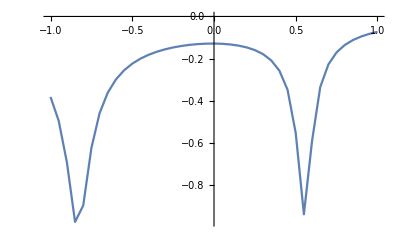

```mathematica
data1=ParallelTable[(y=BetaG1[-1+0.05i];Print[{-1+0.05i,y}];{0.05i-1,y}),{i,0,40}]
ListLinePlot[data1]
```

```mathematica
BetaG2[δ_]:=NIntegrate[Re[Sin[θ]/(2π)^4 D[Tr[PropagatorS2[δ,ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ]].PropagatorS2[δ,ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]]],{q,2}]/.q->0],{ω,-Infinity,Infinity},{θ,0.02,ArcTan[√2]-0.02},{ϕ,0,2π}]+NIntegrate[Re[Sin[θ]/(2π)^4 D[Tr[PropagatorS2[δ,ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ]].PropagatorS2[δ,ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]]],{q,2}]/.q->0],{ω,-Infinity,Infinity},{θ,0.02+ArcTan[√2],π/2-0.02},{ϕ,0,2π}]+NIntegrate[Re[Sin[θ]/(2π)^4 D[Tr[PropagatorS2[δ,ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ]].PropagatorS2[δ,ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]]],{q,2}]/.q->0],{ω,-Infinity,Infinity},{θ,π/2+0.02,(π-ArcTan[√2])-0.02},{ϕ,0,2π}]+NIntegrate[Re[Sin[θ]/(2π)^4 D[Tr[PropagatorS2[δ,ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ]].PropagatorS2[δ,ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]]],{q,2}]/.q->0],{ω,-Infinity,Infinity},{θ,(π-ArcTan[√2])+0.02,π-0.02},{ϕ,0,2π}];
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0936059 and 2.41895×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0446252 and 3.35698×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0974089 and 1.30799×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0446252 and 3.35698×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0974089 and 1.30799×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-0.65,-0.180946}

{-1.,-0.38203}

{-0.6,-0.17293}

{-0.95,-0.323862}

{-0.55,-0.168187}

{-0.5,-0.167267}

{-0.45,-0.171488}

{-0.4,-0.183739}

{-0.9,-0.281675}

{-0.35,-0.210886}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0632916 and 4.31847×10^-7 for the integral and error estimates.

{-0.85,-0.250048}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0632916 and 4.31847×10^-7 for the integral and error estimates.

{-0.3,-0.273127}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.12533 and 2.0064×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-0.8,-0.225765}

{-0.25,-0.463364}

{-0.75,-0.206868}

{-0.2,-1.56939}

{-0.7,-0.192158}

{-0.15,-0.394408}

{0.05,-0.0746947}

{0.1,-0.0620756}

{0.15,-0.0537952}

{0.2,-0.0483517}

{0.25,-0.0448903}

{0.3,-0.042872}

{-0.1,-0.197538}

{0.35,-0.041931}

{0.4,-0.0418083}

{0.45,-0.0423185}

{0.5,-0.0433307}

{0.55,-0.0447551}

{-0.05,-0.128813}

{0.6,-0.0465335}

{0.65,-0.0486322}

{0.,-0.0946343}

{0.7,-0.0510367}

{0.75,-0.053748}

{0.8,-0.0567806}

{0.85,-0.0601615}

{0.9,-0.0639301}

{0.95,-0.0681398}

{1.,-0.0728601}

{{-1.,-0.38203},{-0.95,-0.323862},{-0.9,-0.281675},{-0.85,-0.250048},{-0.8,-0.225765},{-0.75,-0.206868},{-0.7,-0.192158},{-0.65,-0.180946},{-0.6,-0.17293},{-0.55,-0.168187},{-0.5,-0.167267},{-0.45,-0.171488},{-0.4,-0.183739},{-0.35,-0.210886},{-0.3,-0.273127},{-0.25,-0.463364},{-0.2,-1.56939},{-0.15,-0.394408},{-0.1,-0.197538},{-0.05,-0.128813},{0.,-0.0946343},{0.05,-0.0746947},{0.1,-0.0620756},{0.15,-0.0537952},{0.2,-0.0483517},{0.25,-0.0448903},{0.3,-0.042872},{0.35,-0.041931},{0.4,-0.0418083},{0.45,-0.0423185},{0.5,-0.0433307},{0.55,-0.0447551},{0.6,-0.0465335},{0.65,-0.0486322},{0.7,-0.0510367},{0.75,-0.053748},{0.8,-0.0567806},{0.85,-0.0601615},{0.9,-0.0639301},{0.95,-0.0681398},{1.,-0.0728601}}

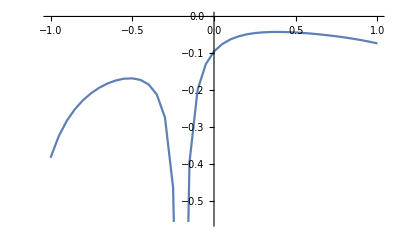

```mathematica
data2=ParallelTable[(y=BetaG2[-1+0.05i];Print[{-1+0.05i,y}];{0.05i-1,y}),{i,0,40}]
ListLinePlot[data2]
```